```mathematica
(*作业1，问题1.1*)
```

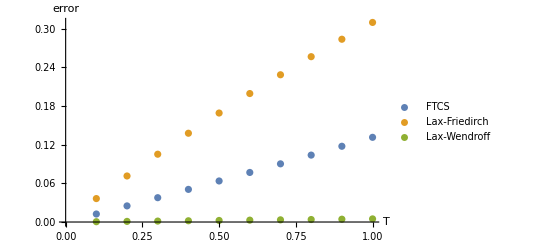

```mathematica
ftcs={{0.1,0.0124164},{0.2,0.0249865},{0.3,0.0377121},{0.4,0.0505952},{0.5,0.0636378},{0.6,0.0768417},{0.7,0.090209},{0.8,0.103742},{0.9,0.117442},{1,0.131311}};
lf={{0.1,0.0363441},{0.2,0.0713681},{0.3,0.10512},{0.4,0.137646},{0.5,0.168991},{0.6,0.199197},{0.7,0.228306},{0.8,0.256357},{0.9,0.283389},{1,0.30944}};
lw={{0.1,0.000484093},{0.2,0.000968172},{0.3,0.00145224},{0.4,0.00193629},{0.5,0.00242033},{0.6,0.00290435},{0.7,0.00338836},{0.8,0.00387235},{0.9,0.00435633},{1,0.00484029}};
ListPlot[{ftcs,lf,lw},PlotLegends->{"FTCS","Lax-Friedirch","Lax-Wendroff"},AxesLabel->{"T","error"}]
```

```mathematica
(*问题1.2*)
```

```mathematica
lw10={{0,-0.272449},{0.1,0.304502},{0.2,0.765143},{0.3,0.933525},{0.4,0.745333},{0.5,0.272449},{0.6,-0.304502},{0.7,-0.765143},{0.8,-0.933525},{0.9,-0.745333},{1,-0.272449}};
lw20={{0,-0.0758226},{0.05,0.233244},{0.1,0.519479},{0.15,0.754863},{0.2,0.916357},{0.25,0.988151},{0.3,0.963217},{0.35,0.843998},{0.4,0.642162},{0.45,0.377467},{0.5,0.0758226},{0.55,-0.233244},{0.6,-0.519479},{0.65,-0.754863},{0.7,-0.916357},{0.75,-0.988151},{0.8,-0.963217},{0.85,-0.843998},{0.9,-0.642162},{0.95,-0.377467},{1,-0.0758226}};
lw40={{0,-0.0192964},{0.025,0.137169},{0.05,0.290256},{0.075,0.436197},{0.1,0.571397},{0.125,0.692527},{0.15,0.796605},{0.175,0.881068},{0.2,0.943836},{0.225,0.983363},{0.25,0.998677},{0.275,0.989401},{0.3,0.955762},{0.325,0.898588},{0.35,0.819289},{0.375,0.719816},{0.4,0.602619},{0.425,0.470583},{0.45,0.32696},{0.475,0.175286},{0.5,0.0192964},{0.525,-0.137169},{0.55,-0.290256},{0.575,-0.436197},{0.6,-0.571397},{0.625,-0.692527},{0.65,-0.796605},{0.675,-0.881068},{0.7,-0.943836},{0.725,-0.983363},{0.75,-0.998677},{0.775,-0.989401},{0.8,-0.955762},{0.825,-0.898588},{0.85,-0.819289},{0.875,-0.719816},{0.9,-0.602619},{0.925,-0.470583},{0.95,-0.32696},{0.975,-0.175286},{1,-0.0192964}};
lw80={{0,-0.00484029},{0.0125,0.0736216},{0.025,0.15163},{0.0375,0.228703},{0.05,0.304366},{0.0625,0.378153},{0.075,0.449608},{0.0875,0.518291},{0.1,0.583779},{0.1125,0.645667},{0.125,0.703575},{0.1375,0.757145},{0.15,0.806047},{0.1625,0.84998},{0.175,0.888672},{0.1875,0.921885},{0.2,0.949414},{0.2125,0.97109},{0.225,0.986779},{0.2375,0.996384},{0.25,0.999846},{0.2625,0.997143},{0.275,0.988293},{0.2875,0.97335},{0.3,0.952406},{0.3125,0.925589},{0.325,0.893067},{0.3375,0.855038},{0.35,0.811737},{0.3625,0.763432},{0.375,0.71042},{0.3875,0.653028},{0.4,0.59161},{0.4125,0.526545},{0.425,0.458233},{0.4375,0.387096},{0.45,0.313573},{0.4625,0.238116},{0.475,0.161191},{0.4875,0.0832724},{0.5,0.00484029},{0.5125,-0.0736216},{0.525,-0.15163},{0.5375,-0.228703},{0.55,-0.304366},{0.5625,-0.378153},{0.575,-0.449608},{0.5875,-0.518291},{0.6,-0.583779},{0.6125,-0.645667},{0.625,-0.703575},{0.6375,-0.757145},{0.65,-0.806047},{0.6625,-0.84998},{0.675,-0.888672},{0.6875,-0.921885},{0.7,-0.949414},{0.7125,-0.97109},{0.725,-0.986779},{0.7375,-0.996384},{0.75,-0.999846},{0.7625,-0.997143},{0.775,-0.988293},{0.7875,-0.97335},{0.8,-0.952406},{0.8125,-0.925589},{0.825,-0.893067},{0.8375,-0.855038},{0.85,-0.811737},{0.8625,-0.763432},{0.875,-0.71042},{0.8875,-0.653028},{0.9,-0.59161},{0.9125,-0.526545},{0.925,-0.458233},{0.9375,-0.387096},{0.95,-0.313573},{0.9625,-0.238116},{0.975,-0.161191},{0.9875,-0.0832724},{1,-0.00484029}};
lw160={{0,-0.00121093},{0.00625,0.0380491},{0.0125,0.0772504},{0.01875,0.116333},{0.025,0.155236},{0.03125,0.193899},{0.0375,0.232264},{0.04375,0.27027},{0.05,0.30786},{0.05625,0.344975},{0.0625,0.381558},{0.06875,0.417552},{0.075,0.452903},{0.08125,0.487556},{0.0875,0.521456},{0.09375,0.554553},{0.1,0.586795},{0.10625,0.618131},{0.1125,0.648515},{0.11875,0.677899},{0.125,0.706237},{0.13125,0.733487},{0.1375,0.759605},{0.14375,0.784553},{0.15,0.80829},{0.15625,0.830781},{0.1625,0.851992},{0.16875,0.871888},{0.175,0.89044},{0.18125,0.907619},{0.1875,0.923399},{0.19375,0.937755},{0.2,0.950665},{0.20625,0.962109},{0.2125,0.972069},{0.21875,0.980531},{0.225,0.987481},{0.23125,0.992908},{0.2375,0.996804},{0.24375,0.999163},{0.25,0.999981},{0.25625,0.999258},{0.2625,0.996994},{0.26875,0.993192},{0.275,0.987859},{0.28125,0.981003},{0.2875,0.972635},{0.29375,0.962766},{0.3,0.951413},{0.30625,0.938593},{0.3125,0.924326},{0.31875,0.908633},{0.325,0.89154},{0.33125,0.873071},{0.3375,0.853257},{0.34375,0.832127},{0.35,0.809714},{0.35625,0.786052},{0.3625,0.761178},{0.36875,0.735131},{0.375,0.70795},{0.38125,0.679677},{0.3875,0.650357},{0.39375,0.620033},{0.4,0.588754},{0.40625,0.556567},{0.4125,0.523521},{0.41875,0.489669},{0.425,0.455061},{0.43125,0.419752},{0.4375,0.383795},{0.44375,0.347247},{0.45,0.310163},{0.45625,0.272601},{0.4625,0.234618},{0.46875,0.196274},{0.475,0.157628},{0.48125,0.118738},{0.4875,0.0796648},{0.49375,0.0404691},{0.5,0.00121093},{0.50625,-0.0380491},{0.5125,-0.0772504},{0.51875,-0.116333},{0.525,-0.155236},{0.53125,-0.193899},{0.5375,-0.232264},{0.54375,-0.27027},{0.55,-0.30786},{0.55625,-0.344975},{0.5625,-0.381558},{0.56875,-0.417552},{0.575,-0.452903},{0.58125,-0.487556},{0.5875,-0.521456},{0.59375,-0.554553},{0.6,-0.586795},{0.60625,-0.618131},{0.6125,-0.648515},{0.61875,-0.677899},{0.625,-0.706237},{0.63125,-0.733487},{0.6375,-0.759605},{0.64375,-0.784553},{0.65,-0.80829},{0.65625,-0.830781},{0.6625,-0.851992},{0.66875,-0.871888},{0.675,-0.89044},{0.68125,-0.907619},{0.6875,-0.923399},{0.69375,-0.937755},{0.7,-0.950665},{0.70625,-0.962109},{0.7125,-0.972069},{0.71875,-0.980531},{0.725,-0.987481},{0.73125,-0.992908},{0.7375,-0.996804},{0.74375,-0.999163},{0.75,-0.999981},{0.75625,-0.999258},{0.7625,-0.996994},{0.76875,-0.993192},{0.775,-0.987859},{0.78125,-0.981003},{0.7875,-0.972635},{0.79375,-0.962766},{0.8,-0.951413},{0.80625,-0.938593},{0.8125,-0.924326},{0.81875,-0.908633},{0.825,-0.89154},{0.83125,-0.873071},{0.8375,-0.853257},{0.84375,-0.832127},{0.85,-0.809714},{0.85625,-0.786052},{0.8625,-0.761178},{0.86875,-0.735131},{0.875,-0.70795},{0.88125,-0.679677},{0.8875,-0.650357},{0.89375,-0.620033},{0.9,-0.588754},{0.90625,-0.556567},{0.9125,-0.523521},{0.91875,-0.489669},{0.925,-0.455061},{0.93125,-0.419752},{0.9375,-0.383795},{0.94375,-0.347247},{0.95,-0.310163},{0.95625,-0.272601},{0.9625,-0.234618},{0.96875,-0.196274},{0.975,-0.157628},{0.98125,-0.118738},{0.9875,-0.0796648},{0.99375,-0.0404691},{1,-0.00121093}};
```

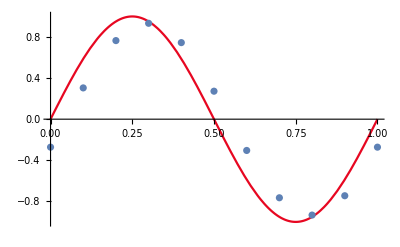

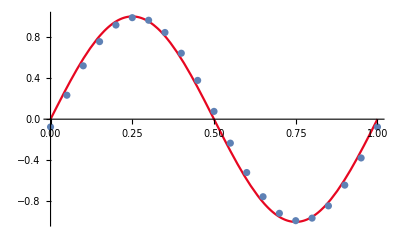

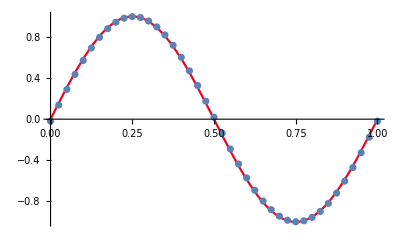

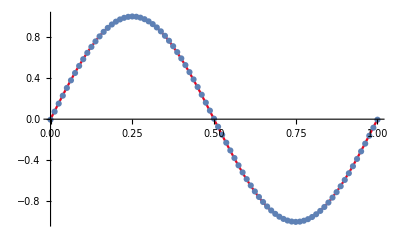

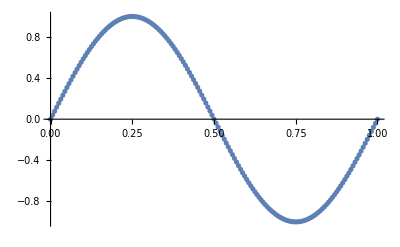

```mathematica
img=Plot[Sin[2 Pi (x+1.0)],{x,0,1},PlotStyle->ColorData[3,"ColorList"]];
img1=ListPlot[lw10];Show[img,img1]
img2=ListPlot[lw20];Show[img,img2]
img3=ListPlot[lw40];Show[img,img3]
img4=ListPlot[lw80];Show[img,img4]
img5=ListPlot[lw160];Show[img,img5]
```

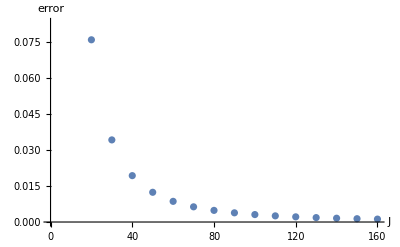

```mathematica
lwj={{10,0.283284},{20,0.0758226},{30,0.0341659},{40,0.0192964},{50,0.0123706},{60,0.00859807},{70,0.00632006},{80,0.00484029},{90,0.00382521},{100,0.00309887},{110,0.00256131},{120,0.00215238},{130,0.00183409},{140,0.00158151},{150,0.00137772},{160,0.00121093}};
ListPlot[lwj,AxesLabel->{"J","error"}]
```